# Escape time versus initial shooting angle for some values of b

```mathematica
SetDirectory[NotebookDirectory[]];
```

Here we collect the plots in “EscapeTimeScatteringFunction.nb”

```mathematica
l[b_]:=If[$IsPositive,-3b+√(3+144 b^2),-3b-√(3+144 b^2)];
εcrit[b_]:=√(1+4 b Abs[l[b]]);
```

## Positive l (ε=1.2)

```mathematica
ε=1.2;
```

## b=0.1

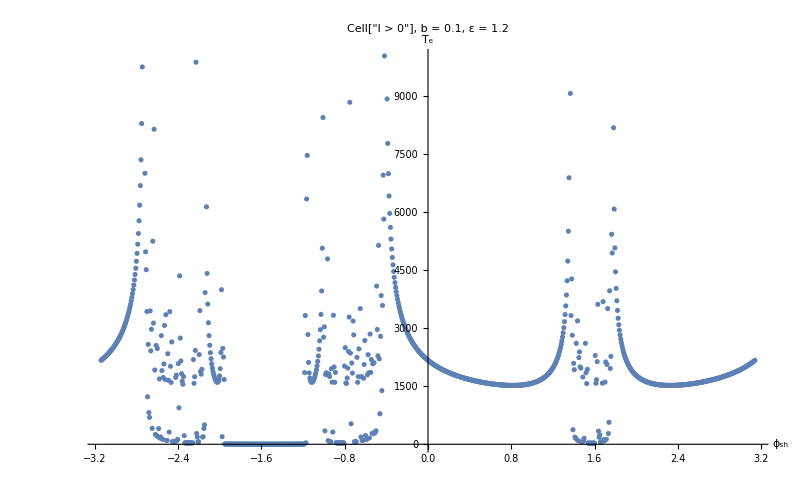

pl_b(01)_e(12)_1.png

```mathematica
b=0.1;dataPts=Import["pl_b(01)_e(12)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"6444d261-8c37-483f-9592-98551b793bf0"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(12)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

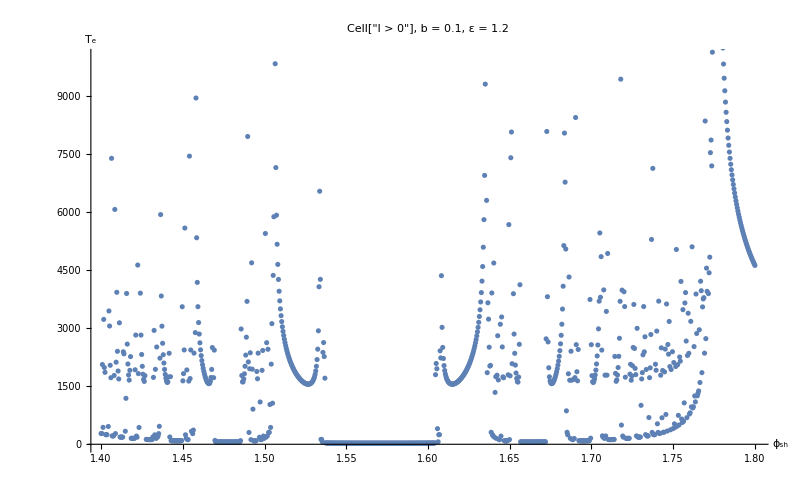

pl_b(01)_e(12)_2.png

```mathematica
dataPts=Import["pl_b(01)_e(12)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"cc4d9692-aae4-479e-bece-7dbd69f1435d"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(12)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

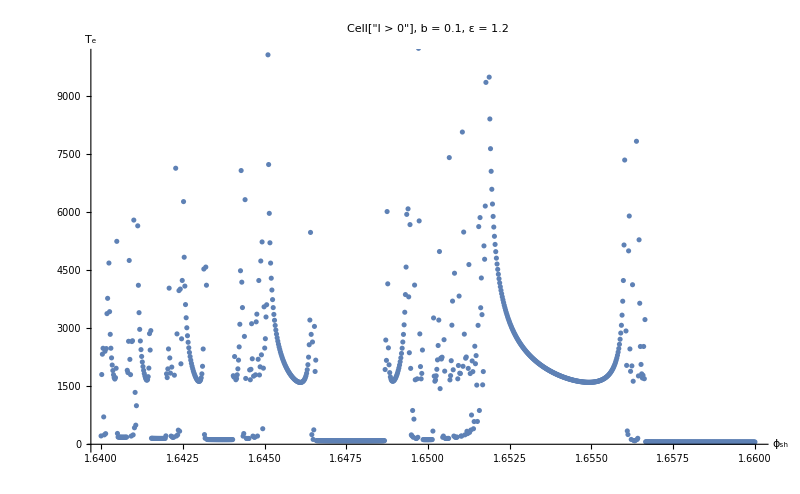

pl_b(01)_e(12)_3.png

```mathematica
dataPts=Import["pl_b(01)_e(12)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"a157ee50-34f4-452d-b0ec-3ec6f73b44d6"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(12)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## b=0.5

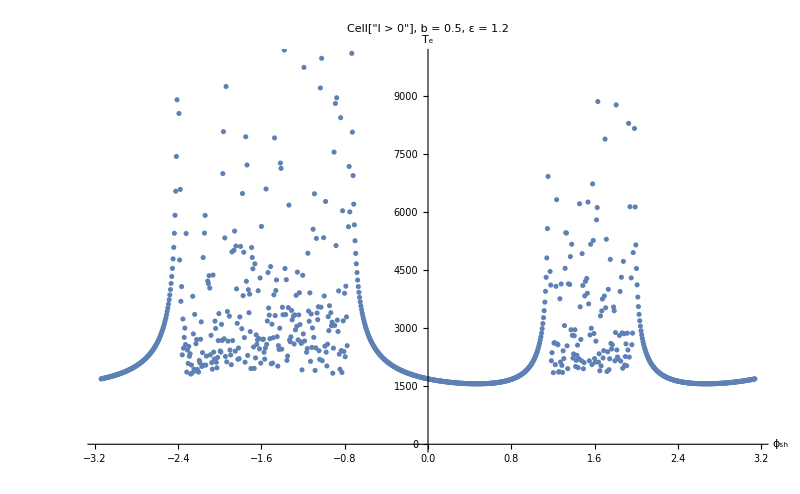

pl_b(05)_e(12)_1.png

```mathematica
b=0.5;dataPts=Import["pl_b(05)_e(12)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"5a247f4a-ffd0-4afd-b8b4-1205294b25fd"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(12)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

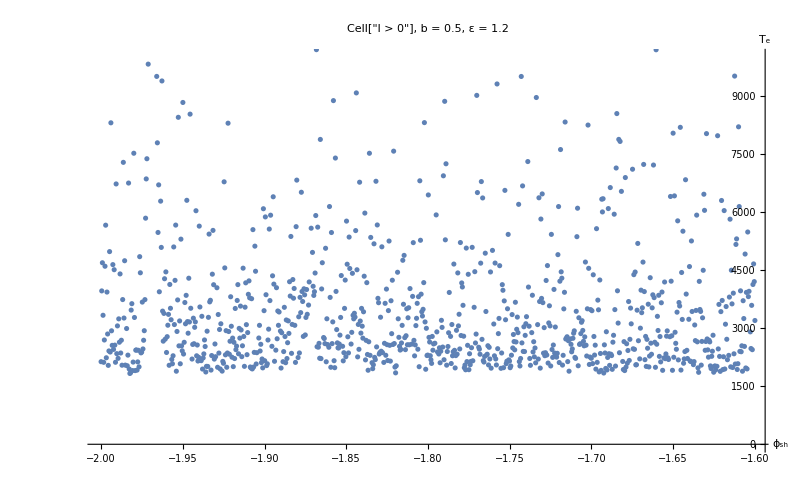

pl_b(05)_e(12)_2.png

```mathematica
dataPts=Import["pl_b(05)_e(12)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"a91dfcf8-45a9-483b-b61a-be258e1f2674"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(12)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

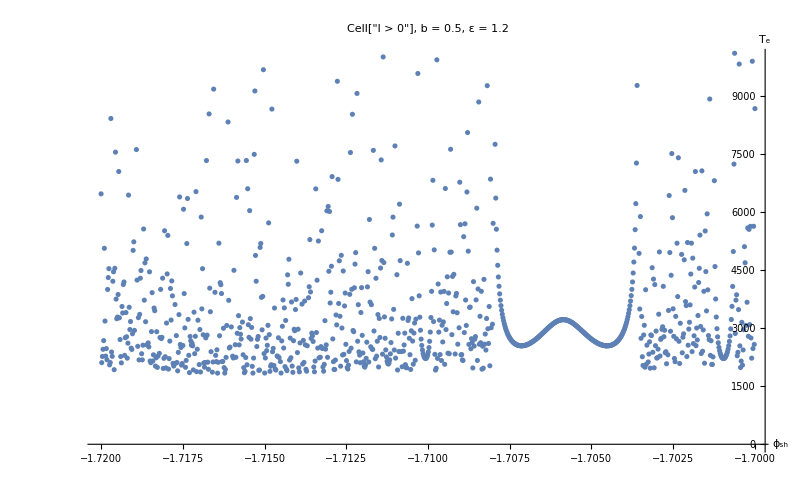

pl_b(05)_e(12)_3.png

```mathematica
dataPts=Import["pl_b(05)_e(12)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"9385dab4-bb25-494a-b81d-eeeb30192433"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(12)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## Positive l (ε=3.0)

```mathematica
ε=3;
```

## b=0.1

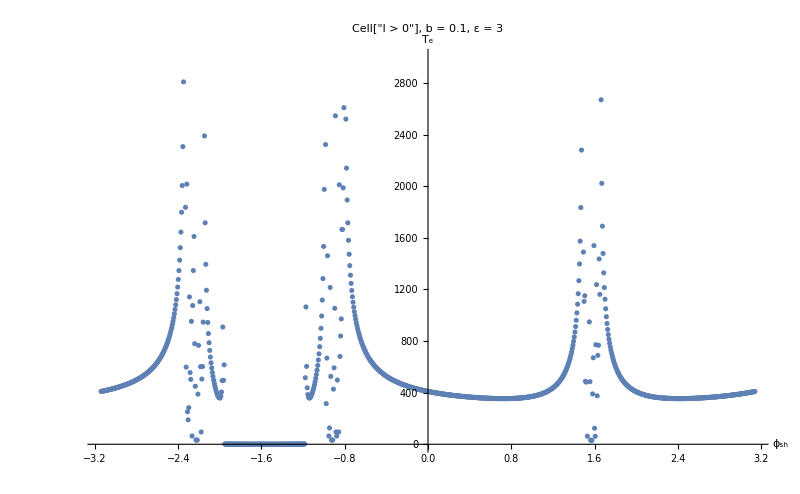

pl_b(01)_e(30)_1.png

```mathematica
b=0.1;dataPts=Import["pl_b(01)_e(30)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,3000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"42fca92d-4075-484a-814d-b3bb4c9d4827"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(30)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

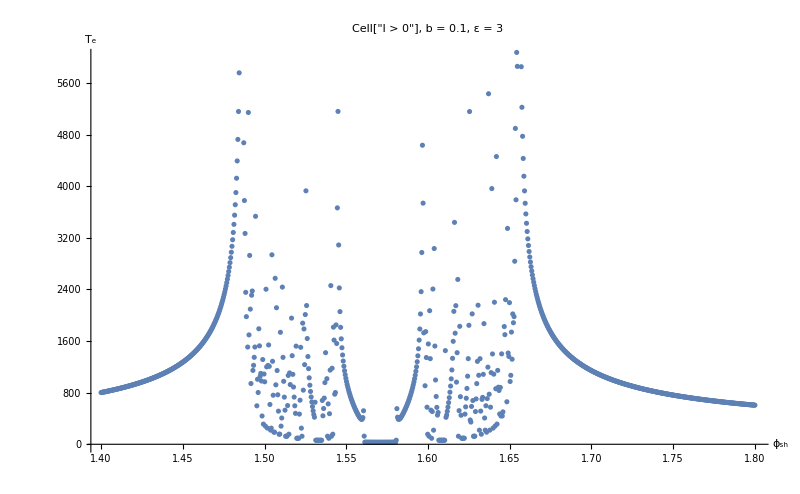

pl_b(01)_e(30)_2.png

```mathematica
dataPts=Import["pl_b(01)_e(30)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"33638817-cca2-4e3b-9b32-960e9191837b"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(30)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

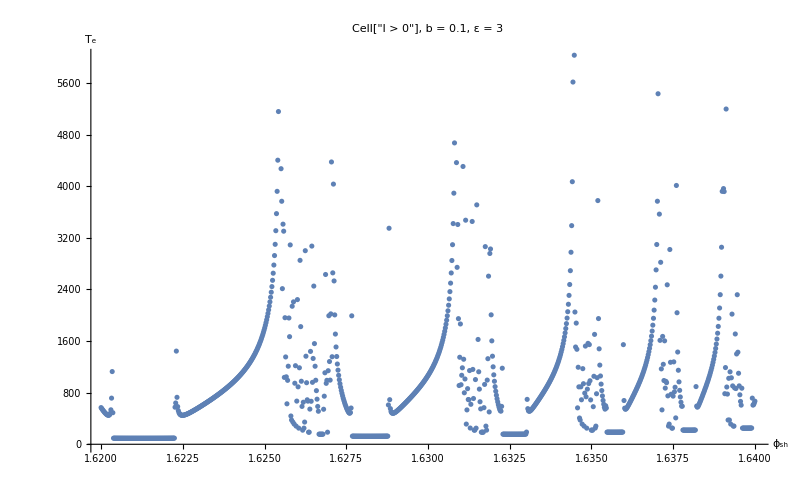

pl_b(01)_e(30)_3.png

```mathematica
dataPts=Import["pl_b(01)_e(30)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"78a7c347-7ef1-44fc-9a4d-36cd52bb29ab"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(01)_e(30)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## b=0.5

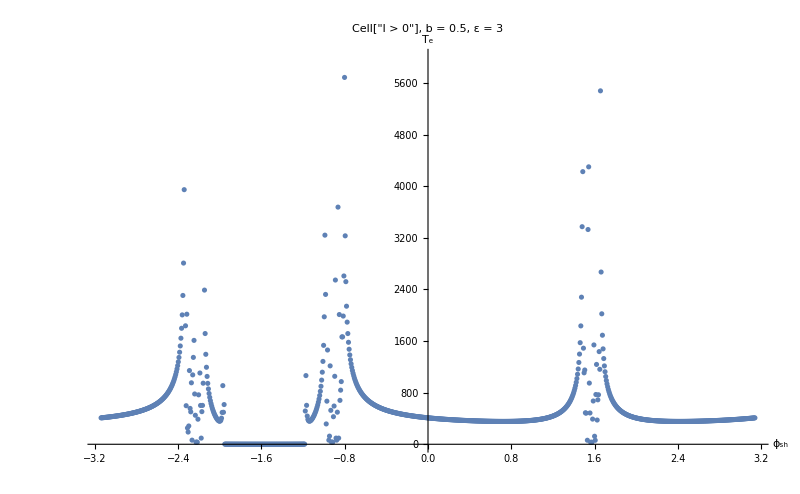

pl_b(05)_e(30)_1.png

```mathematica
b=0.5;dataPts=Import["pl_b(05)_e(30)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"a8cb7696-bab0-4f28-a5d8-1b186cb3998b"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(30)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

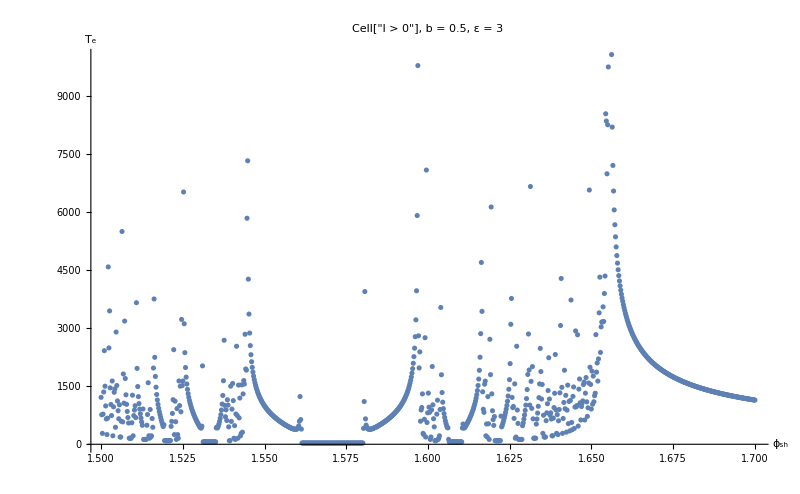

pl_b(05)_e(30)_2.png

```mathematica
dataPts=Import["pl_b(05)_e(30)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"61d3fbc9-55de-4071-8f19-684d9e728d12"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(30)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

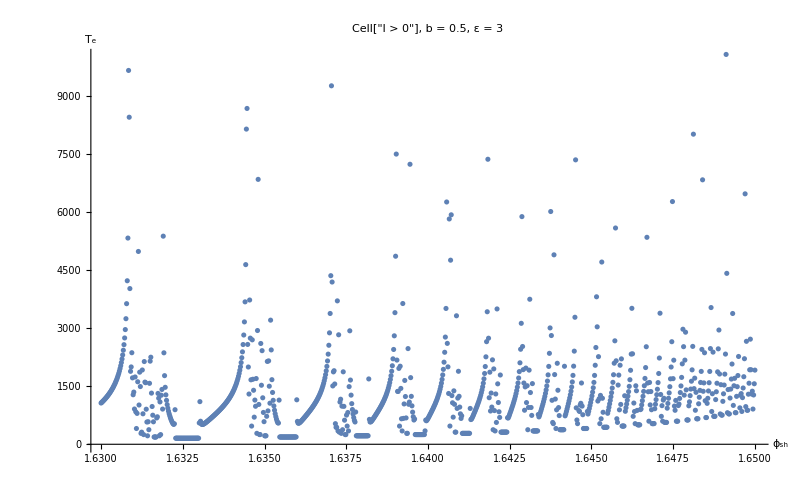

pl_b(05)_e(30)_3.png

```mathematica
dataPts=Import["pl_b(05)_e(30)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l > 0",ExpressionUUID->"91dde60d-7af8-4e8e-9514-a492657f23e7"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["pl_b(05)_e(30)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## Negative l (ε=ε_crit+0.2)

```mathematica
$IsPositive=False;
```

## b=0.01

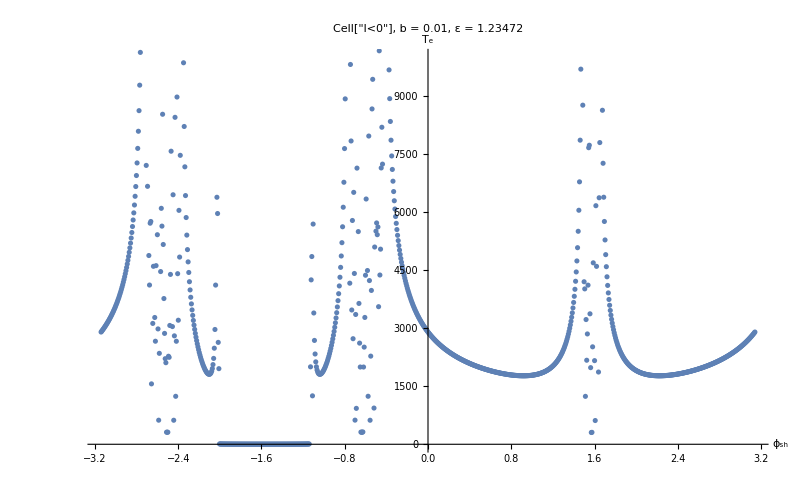

ml_b(001)_e(ecrit_02)_1.png

```mathematica
b=0.01;ε=εcrit[b]+0.2;dataPts=Import["ml_b(001)_e(ecrit_02)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"01c1c34d-912c-431f-9ae7-be141eb6d8e3"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_02)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

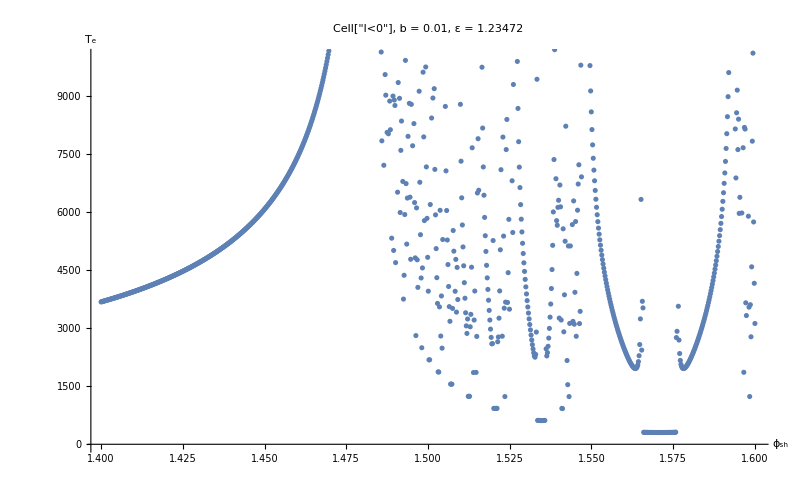

ml_b(001)_e(ecrit_02)_2.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_02)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"f307cd19-bd48-4a7f-b692-72785178a3dd"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_02)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

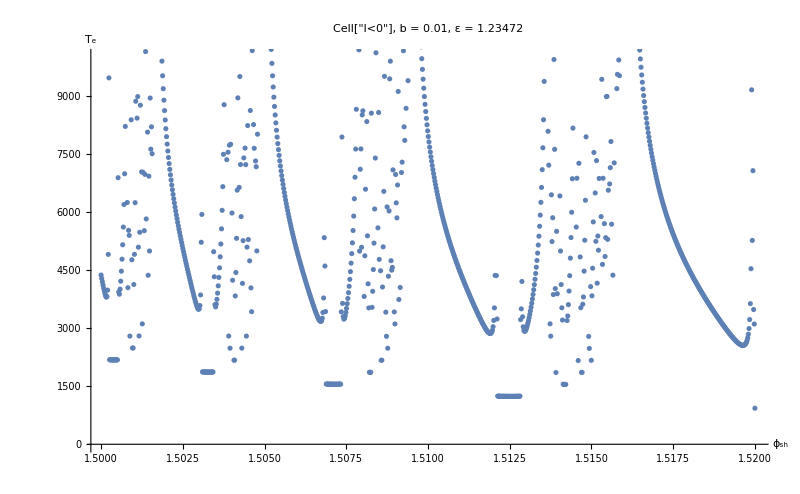

ml_b(001)_e(ecrit_02)_3.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_02)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"f7c09ff4-bc50-47a1-9c12-9505bb7173c1"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_02)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## b=0.1

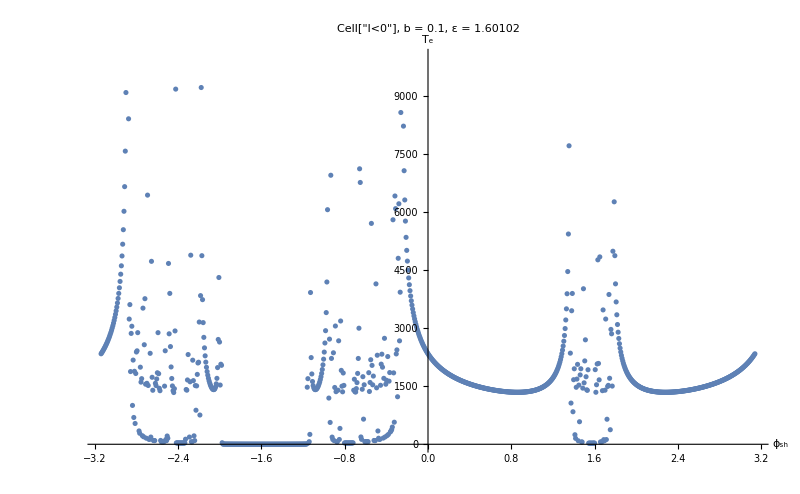

ml_b(01)_e(ecrit_02)_1.png

```mathematica
b=0.1;ε=εcrit[b]+0.2;dataPts=Import["ml_b(01)_e(ecrit_02)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"d0185bc6-d4ad-4d01-b696-7154ea8b0dac"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_02)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

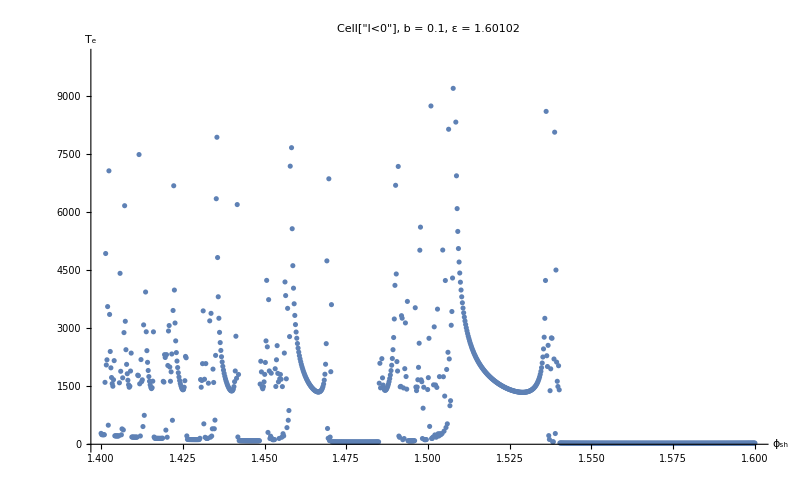

ml_b(01)_e(ecrit_02)_2.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_02)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"f0a7b2a1-cf51-4cbf-afe8-6f214a413c8c"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_02)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

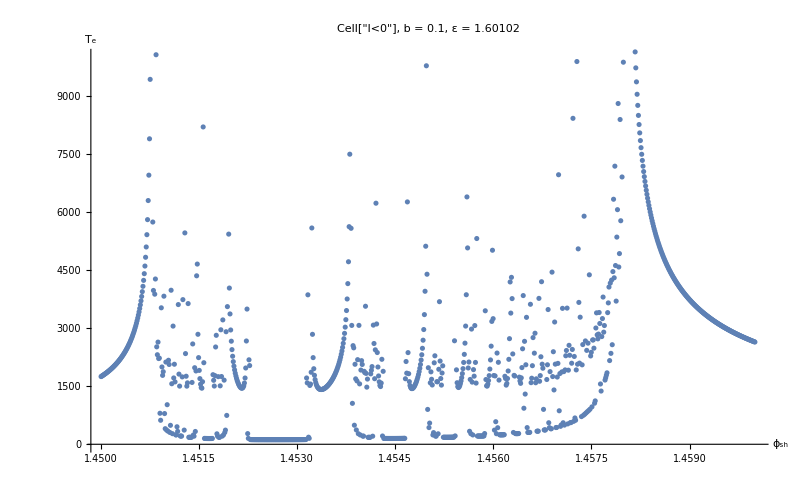

ml_b(01)_e(ecrit_02)_3.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_02)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"33503b3c-17fd-4e1d-9dfa-171aae1cdf33"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_02)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## b=0.5

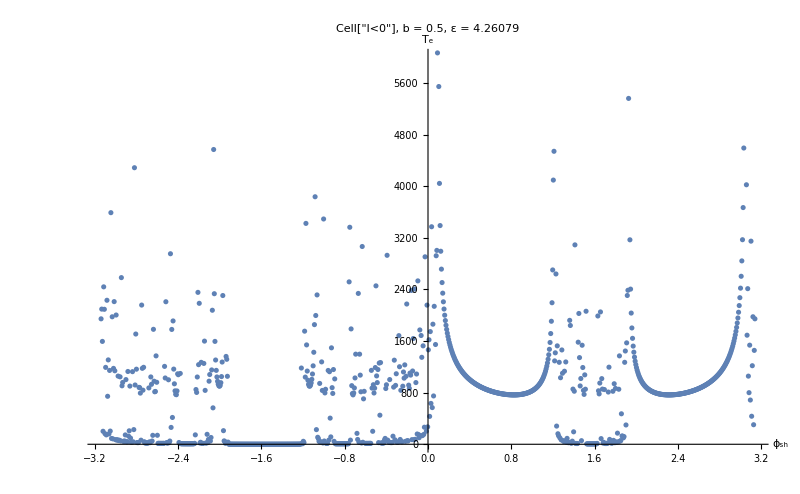

ml_b(05)_e(ecrit_02)_1.png

```mathematica
b=0.5;ε=εcrit[b]+0.2;dataPts=Import["ml_b(05)_e(ecrit_02)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"5e7e006a-52b6-4db9-8141-9cce88164334"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_02)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

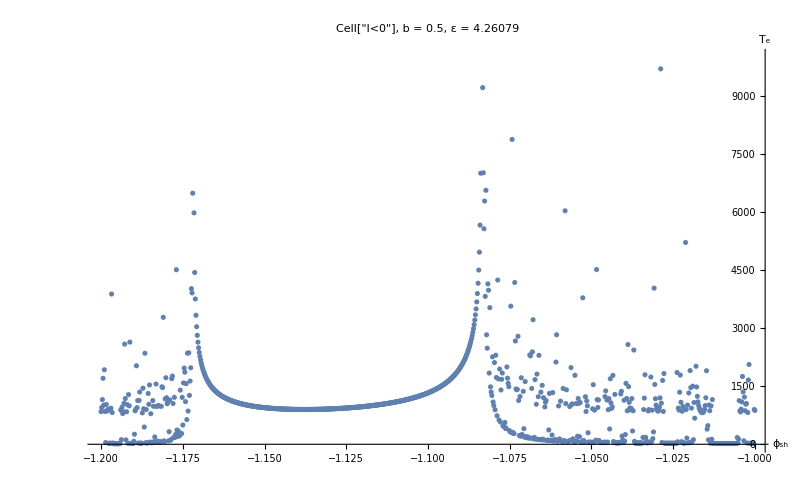

ml_b(05)_e(ecrit_02)_2.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_02)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"e15181c1-0153-46be-853d-ba247eb4ea1c"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_02)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

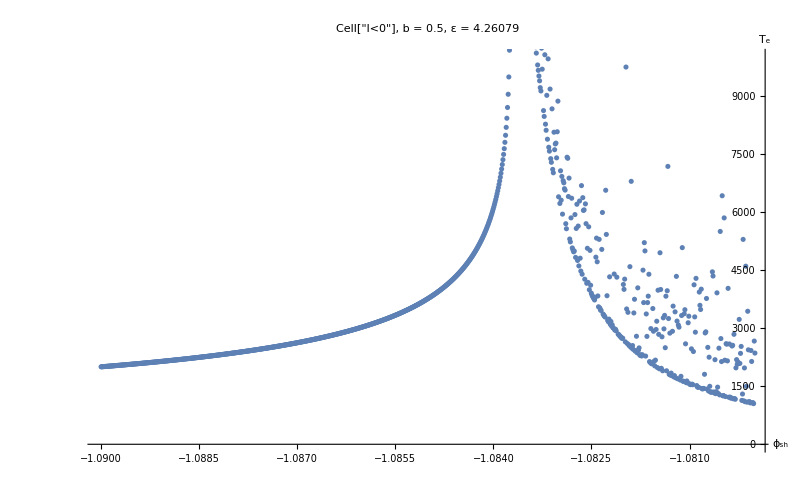

ml_b(05)_e(ecrit_02)_3.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_02)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"87185cfa-7739-4d38-beb1-5aa56f9c7ef5"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_02)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## Negative l (ε=ε_crit+2)

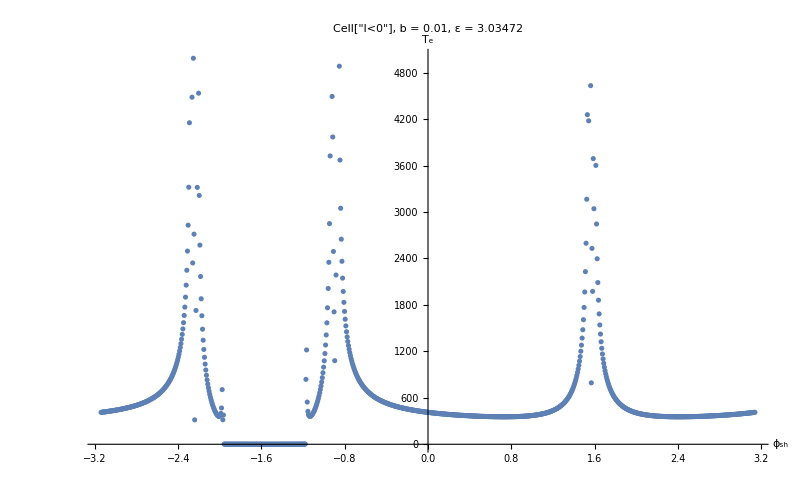

ml_b(001)_e(ecrit_2)_1.png

```mathematica
b=0.01;ε=εcrit[b]+2;dataPts=Import["ml_b(001)_e(ecrit_2)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,5000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"63293c39-3e0a-4930-8766-fa9a4a55d5a1"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_2)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

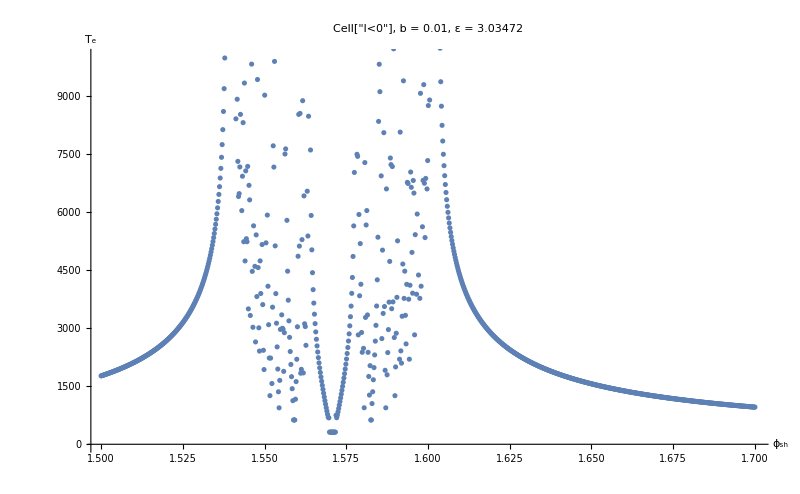

ml_b(001)_e(ecrit_2)_2.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_2)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"b6859580-eea7-4f7d-821a-2a607309a71d"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_2)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

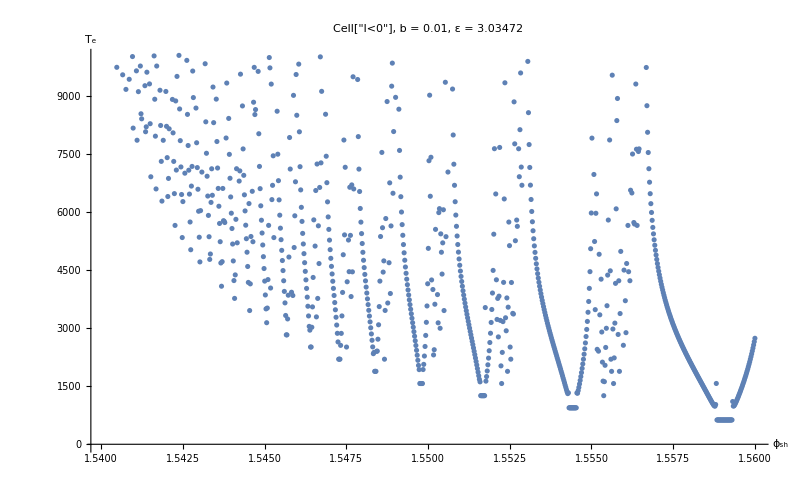

ml_b(001)_e(ecrit_2)_3.png

```mathematica
dataPts=Import["ml_b(001)_e(ecrit_2)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"b81e3e41-4022-48b9-9245-a15fcab68148"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(001)_e(ecrit_2)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## b=0.1

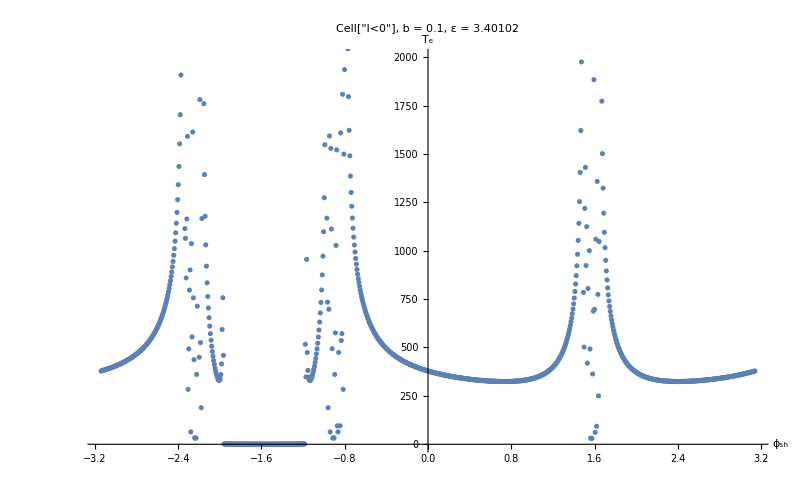

ml_b(01)_e(ecrit_2)_1.png

```mathematica
b=0.1;ε=εcrit[b]+2;dataPts=Import["ml_b(01)_e(ecrit_2)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,2000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"a5ad68e1-3877-44e0-ada3-10f7e77a967e"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_2)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

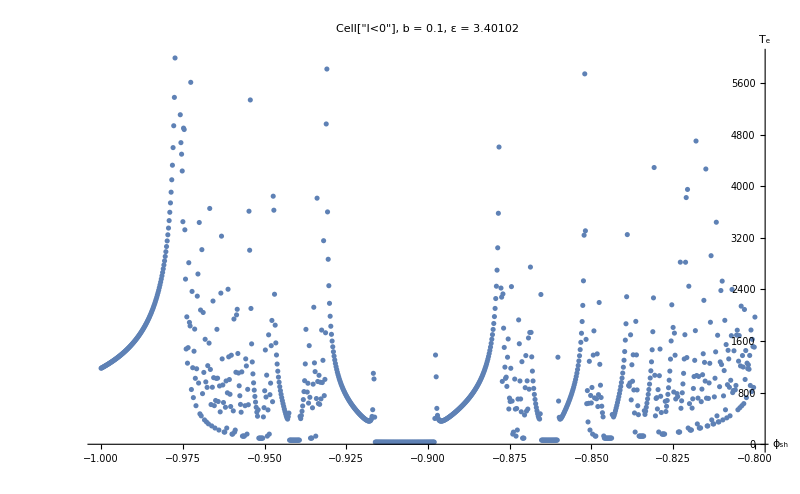

ml_b(01)_e(ecrit_2)_2.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_2)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"c76255b3-d5fc-4f1f-bc41-a08051a5a002"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_2)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

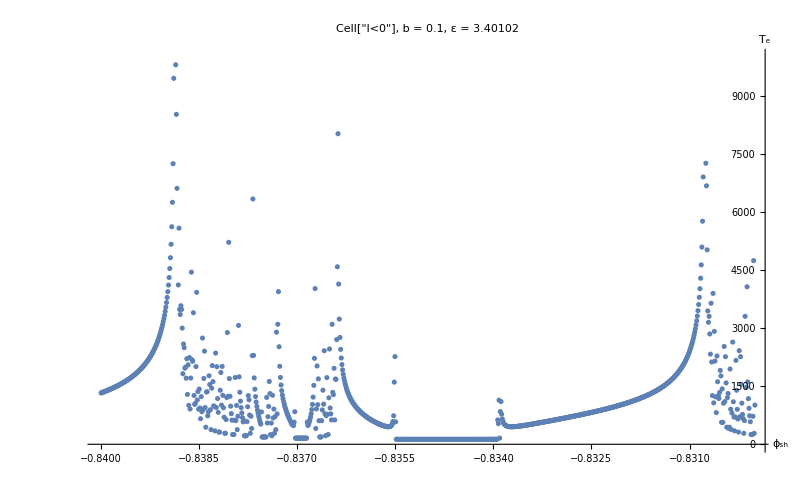

ml_b(01)_e(ecrit_2)_3.png

```mathematica
dataPts=Import["ml_b(01)_e(ecrit_2)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"7c95eba2-3cdf-4d38-b267-1a13774c8f32"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(01)_e(ecrit_2)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

## b=0.5

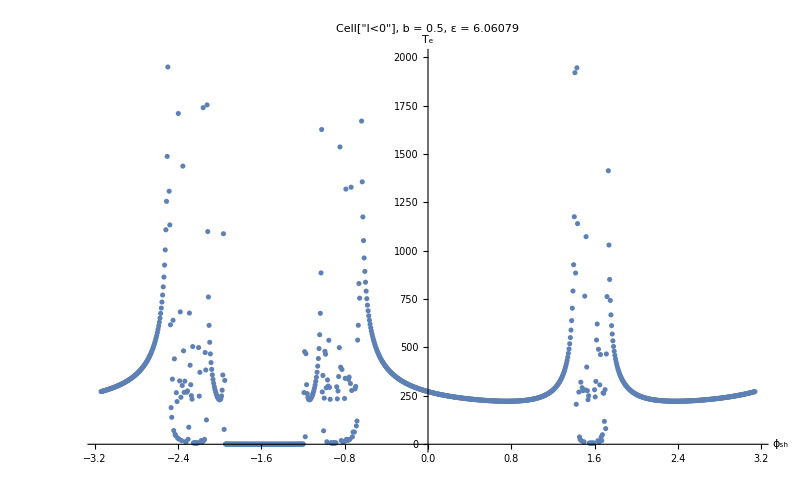

ml_b(05)_e(ecrit_2)_1.png

```mathematica
b=0.5;ε=εcrit[b]+2;dataPts=Import["ml_b(05)_e(ecrit_2)_1.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,2000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"15b431f3-d820-452f-9284-2c258a093870"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_2)_1.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

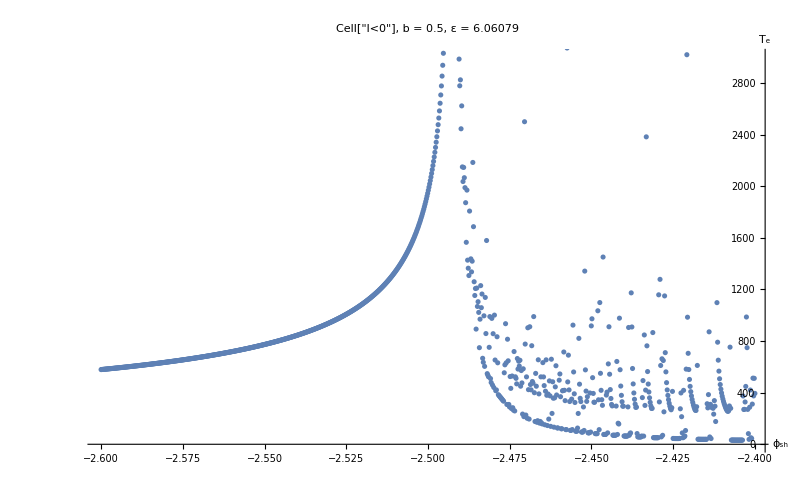

ml_b(05)_e(ecrit_2)_2.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_2)_2.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,3000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"dd5ebda8-30d0-423f-84cc-a5ea5cd30db2"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_2)_2.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```

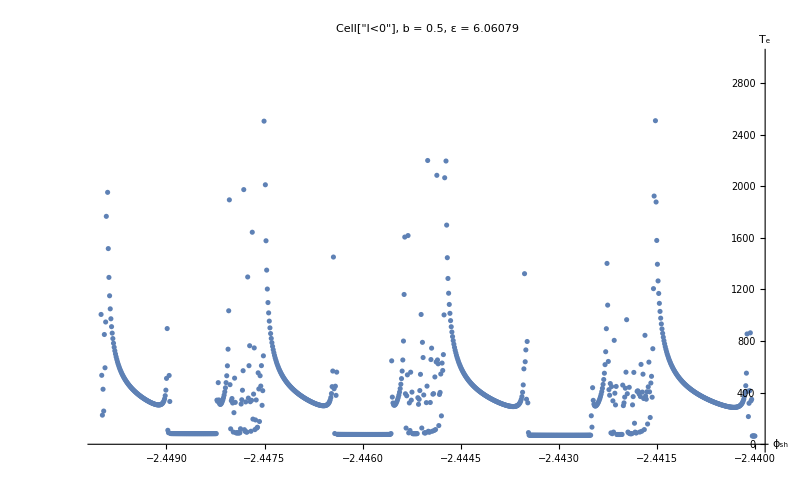

ml_b(05)_e(ecrit_2)_3.png

```mathematica
dataPts=Import["ml_b(05)_e(ecrit_2)_3.mx"];
plot=ListPlot[dataPts,PlotRange->{All,{0,3000}},PlotLabel->StringJoin["Cell["l<0",ExpressionUUID->"e79a13d9-a61c-4767-9d16-a1e0113fd6b0"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"}];
Show[plot,LabelStyle->{FontSize->12},ImageSize->800]
Export["ml_b(05)_e(ecrit_2)_3.png",Show[plot,LabelStyle->{FontSize->40},ImageSize->2000]]
```